```mathematica
sc1=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\AB.csv"];
scMerge=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\merge.csv"];
scTop=Import["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\AB_Top.csv"];
```

```mathematica
Grid[sc1,Frame->All];
Grid[scMerge,Frame->All];
Grid[scTop,Frame->All];
```

```mathematica
Union[sc1[[;;,2]]];
Union[scMerge[[;;,4]]];
Union[scTop[[;;,2]]]
```

{ABBIE,BOBBY,JERRY,JUDGE HOFFMAN,KUNSTLER,RENNIE,SCHULTZ,Speaker,TOM,WEINGLASS}

```mathematica
SortBy[Tally[sc1[[;;,2]]],Last];
```

```mathematica
SortBy[Tally[scMerge[[;;,4]]],Last];
```

```mathematica
SortBy[Tally[scTop[[;;,2]]],Last]
```

{{Speaker,1},{WEINGLASS,41},{RENNIE,51},{BOBBY,59},{JERRY,91},{SCHULTZ,99},{ABBIE,113},{JUDGE HOFFMAN,134},{TOM,154},{KUNSTLER,189}}

```mathematica
ch = sc1[[;;,2]];
chMerge= scMerge[[;;,4]];
chTop= scTop[[;;,2]];
```

```mathematica
e1=Table[ch[[i]]<->ch[[i+1]],{i,1,Length[ch]-1}];
e2=Table[ch[[i]]->ch[[i+1]],{i,1,Length[ch]-1}];

e1Mrg=Table[chMerge[[i]]<->chMerge[[i+1]],{i,1,Length[chMerge]-1}];
e2Mrg=Table[chMerge[[i]]->chMerge[[i+1]],{i,1,Length[chMerge]-1}];

e1Top=Table[chTop[[i]]<->chTop[[i+1]],{i,1,Length[chTop]-1}];
e2Top=Table[chTop[[i]]->chTop[[i+1]],{i,1,Length[chTop]-1}];
```

```mathematica
v1 = Union[ch];
v1Mrg = Union[chMerge]; 
v1Top= Union[chTop];
```

```mathematica
<->
```

```mathematica
UndirectedWeightedGraph1=Graph[v1,e1,VertexLabels->"Name"] ;
UndirectedNonWeightedGraph2=SimpleGraph[UndirectedWeightedGraph1];
DirectedWeightedGraph3=Graph[v1,e2,VertexLabels->"Name"];
DirectedNonWeightedGraph4=SimpleGraph[DirectedWeightedGraph3];

MergeUndirectedWeightedGraph1=Graph[v1Mrg,e1Mrg,VertexLabels->"Name", ImageSize->Full];
```

```mathematica
s1
```

s1

```mathematica
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph1.jpg", UndirectedWeightedGraph1]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph2.jpg", UndirectedNonWeightedGraph2]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph3.jpg", DirectedWeightedGraph3]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\graph4.jpg", DirectedNonWeightedGraph4]
```

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph1.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph2.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph3.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\graph4.jpg

```mathematica
DegreeCentrality[UndirectedWeightedGraph1];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],DegreeCentrality[UndirectedWeightedGraph1]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedNonWeightedGraph2],DegreeCentrality[UndirectedNonWeightedGraph2]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedWeightedGraph3],DegreeCentrality[DirectedWeightedGraph3]}],Last]
```

{{Speaker,1},{BARTENDER,2},{CROWD MEMBER,2},{DALEY,2},{DELEGATE,2},{DEMONSTRATOR,2},{FRAT BOY #1,2},{FRAT BOY #2,2},{GOVERNMENT OFFICIAL,2},{JACK,2},{LYNDON JOHNSON,2},{MAN,2},{MARJORIE,2},{MARSHAL,2},{MARTIN LUTHER KING,2},{MRS. DELLINGER,2},{MRS. WINTER,2},{OFFICER,2},{OFFICER #2,2},{OFFICER QUINN,2},{PATRONS,2},{POLICE OFFICER,2},{PROTESTORS,2},{REPORTER,2},{REPORTER #1,2},{REPORTER #2,2},{REPORTER #3,2},{REPORTER #4,2},{REPORTER #5,2},{REPORTER #6,2},{REPORTER #7,2},{REPORTER #8,2},{REPORTER #9,2},{ROBERT KENNEDY,2},{SOMEONE IN THE CROWD,2},{SONDRA,2},{STUDENT,2},{SY,2},{WALTER CRONKITE,2},{WOMAN,2},{ALL,3},{CROWD,3},{SON,3},{BAR PATRON #1,4},{BELL,4},{EDDIE,4},{FRAPOLY,4},{JANE,4},{JUROR #6,4},{SECRETARY,4},{YOUNG MAN,4},{FRAT BOYS,5},{MITCHELL,5},{BAR PATRON #2,6},{FRED,6},{POLICEMAN,6},{SAM,6},{SCOTT,6},{BAILIFF,7},{WOJOHOWSKI,7},{WEINER,8},{DELUCA,10},{FROINES,10},{BERNADINE,11},{HOWARD,11},{STAHL,11},{FORAN,12},{CLARK,13},{DAPHNE,14},{BOBBY,15},{RENNIE,21},{DAVE,22},{WEINGLASS,24},{JUDGE HOFFMAN,31},{TOM,36},{SCHULTZ,38},{JERRY,39},{ABBIE,48},{KUNSTLER,54}}

```mathematica
SortBy[Transpose[{VertexList[DirectedNonWeightedGraph4],DegreeCentrality[DirectedNonWeightedGraph4]}],Last];
```

```mathematica
PageRankCentrality[UndirectedWeightedGraph1,0.85];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],PageRankCentrality[UndirectedWeightedGraph1,0.85]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedNonWeightedGraph2],PageRankCentrality[UndirectedNonWeightedGraph2,0.85]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedWeightedGraph3],PageRankCentrality[DirectedWeightedGraph3,0.85]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedNonWeightedGraph4],PageRankCentrality[DirectedNonWeightedGraph4,0.85]}],Last];

ClosenessCentrality[UndirectedWeightedGraph1];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],ClosenessCentrality[UndirectedWeightedGraph1]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[UndirectedNonWeightedGraph2],ClosenessCentrality[UndirectedNonWeightedGraph2]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedWeightedGraph3],ClosenessCentrality[DirectedWeightedGraph3]}],Last];
```

```mathematica
SortBy[Transpose[{VertexList[DirectedNonWeightedGraph4],ClosenessCentrality[DirectedNonWeightedGraph4]}],Last];
```

## 2) compute the 4 graph on the merge.csv file (AB-srt.csv)

```mathematica
MrgUndirectedWeightedGraph1=Graph[v1Mrg,e1Mrg,VertexLabels->"Name",ImageSize->Full] ;
MrgUndirectedNonWeightedGraph2=SimpleGraph[MrgUndirectedWeightedGraph1, ImageSize->Full];
MrgDirectedWeightedGraph3=Graph[v1Mrg,e2Mrg,VertexLabels->"Name", ImageSize->Full];
MrgDirectedNonWeightedGraph4=SimpleGraph[MrgDirectedWeightedGraph3, ImageSize->Full];
```

Export pictures

```mathematica
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph1.jpg", UndirectedWeightedGraph1]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph2.jpg", UndirectedNonWeightedGraph2]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph3.jpg", DirectedWeightedGraph3]
Export["C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\Mrg_graph4.jpg", DirectedNonWeightedGraph4]
```

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph1.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph2.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph3.jpg

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\Mrg_graph4.jpg

## New AB graph of 8 peopl:

PREPARE grapfh of 8 charcters Undirect and Direct - (both weighted)

```mathematica
UndirectedWeightedGraph1;
DirectedWeightedGraph3;
```

```mathematica
namesUnDirect=Take[SortBy[Transpose[{VertexList[UndirectedWeightedGraph1],VertexDegree[UndirectedWeightedGraph1]}],Last],{-10,-1}][[;;,1]];
namesDirect=Take[SortBy[Transpose[{VertexList[DirectedWeightedGraph3],VertexDegree[DirectedWeightedGraph3]}],Last],{-10,-1}][[;;,1]]
```

{DAVE,WEINGLASS,RENNIE,BOBBY,JERRY,SCHULTZ,ABBIE,JUDGE HOFFMAN,TOM,KUNSTLER}

```mathematica
{"DAVE","WEINGLASS","RENNIE","BOBBY","JERRY","SCHULTZ","ABBIE","JUDGE HOFFMAN","TOM","KUNSTLER"}
```

{DAVE,WEINGLASS,RENNIE,BOBBY,JERRY,SCHULTZ,ABBIE,JUDGE HOFFMAN,TOM,KUNSTLER}

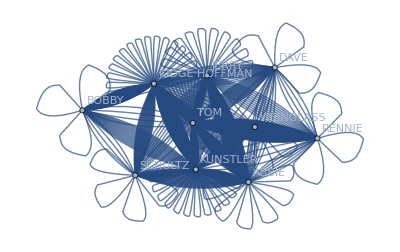

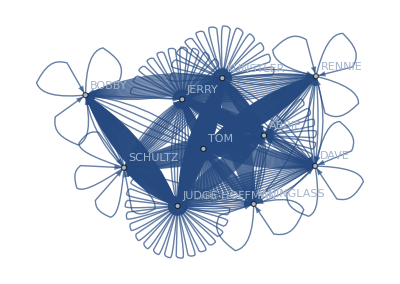

C:\Users\matane\Desktop\לימודים\סמסטר ח\The_Trial_of_the_Chicago_Analyzing\test.jpg

```mathematica
TopgGrapUndirect1=Subgraph[UndirectedWeightedGraph1,namesUnDirect,VertexLabels->"Name"]
TopgGrapDirect3=Subgraph[DirectedWeightedGraph3,namesDirect,VertexLabels->"Name"]
"C:\\Users\\matane\\Desktop\\לימודים\\סמסטר ח\\The_Trial_of_the_Chicago_Analyzing\\test.jpg"
```

### TRANFORM frequency to distance matrix
To Transform the frequency graph to metric space, we have two steps the first step is to transform the frequency into a distance then we convert the space to a metric space using “Dijkstra”, “FloydWarshall.”

### The function we use

```mathematica
FromFrequencyGraph2Distances[G_]:=
(* The input of the function is a frequency graph G the output is a distances matrix*)
Module[{i,j,A,W,n},
(* i,j are Indexes. 
n is the number of nodes in athe G. 
A is the Adjacency Matrix of G 
 W is the distances matrix
*)
A=AdjacencyMatrix[G];
n=Length[A];
W=Table[If[i==j,0,
If[A[[i,j]]== 0,Infinity,
1/A[[i,j]]]],{i,1,n},{j,1,n}]; (* Computing the distances matrix W*)
W
];
FromFrequencyGraph2Metricspace[G_]:=
(* The input is a frequency graph G
  The output dis is a distances matrix of the Metricspace
 *)
Module[{dis1,G1,dis},
dis1=FromFrequencyGraph2Distances[G]; (* Converts the frequencies in G to distances matrix*)
G1=WeightedAdjacencyGraph[dis1]; (* Converts dis1 distances matrix to Weighted Adjacency Graph*)
dis=GraphDistanceMatrix[G1] (* Output the distances matrix of the Metricspace *)
];
```

```mathematica
MatUnDirect = FromFrequencyGraph2Metricspace[TopgGrapUndirect1];
MatrixForm[MatUnDirect]
```

(0. | 0.12152 | 0.0725047 | 0.101463 | 0.105556 | 0.11962 | 0.0825826 | 0.0845139 | 0.0555556 | 0.0688889
0.12152 | 0. | 0.0829141 | 0.0852057 | 0.114059 | 0.108257 | 0.0896686 | 0.0682566 | 0.0659649 | 0.0526316
0.0725047 | 0.0829141 | 0. | 0.0628566 | 0.0669492 | 0.0810132 | 0.0439762 | 0.0459075 | 0.0169492 | 0.0302825
0.101463 | 0.0852057 | 0.0628566 | 0. | 0.093971 | 0.0569492 | 0.0695807 | 0.0169492 | 0.0459075 | 0.0325742
0.105556 | 0.114059 | 0.0669492 | 0.093971 | 0. | 0.0614273 | 0.0243902 | 0.0770218 | 0.05 | 0.0614273
0.11962 | 0.108257 | 0.0810132 | 0.0569492 | 0.0614273 | 0. | 0.037037 | 0.04 | 0.0640641 | 0.055625
0.0825826 | 0.0896686 | 0.0439762 | 0.0695807 | 0.0243902 | 0.037037 | 0. | 0.0526316 | 0.027027 | 0.037037
0.0845139 | 0.0682566 | 0.0459075 | 0.0169492 | 0.0770218 | 0.04 | 0.0526316 | 0. | 0.0289583 | 0.015625
0.0555556 | 0.0659649 | 0.0169492 | 0.0459075 | 0.05 | 0.0640641 | 0.027027 | 0.0289583 | 0. | 0.0133333
0.0688889 | 0.0526316 | 0.0302825 | 0.0325742 | 0.0614273 | 0.055625 | 0.037037 | 0.015625 | 0.0133333 | 0.)

(we write the index of name for conveints use)

```mathematica
VertexIndex[TopgGrapUndirect1, {"DAVE","WEINGLASS","RENNIE","BOBBY","JERRY","SCHULTZ","ABBIE","JUDGE HOFFMAN","TOM","KUNSTLER"}]
```

{1,2,3,4,5,6,7,8,9,10}

## Now we import 2  function help for voting algorithm

```mathematica
Dis2Set[dis_,S1_,p_]:=
(* The input is a distances matrix of the metricspace dis, a subset of indexes S1, and a index p of a point in the metricspace
  The output is the distans of p to s1
 *)
Min[dis[[p]][[S1]]];
```

```mathematica
FromMetricspaceS2DecisionMatric[dis_,V1_]:=
(* 
 The input is a distances matrix of the metricspace dis, A a set of disjoint k subsets V1
The Decision Matrix ψ
*)
Module[{n,k,i,j,ψ},
(*
  n is the number of nodes in the metricspace.
k is the number of options in the Decision Matrix output. 
i,j are indexes
 ψ is the Decision Matrix output 
*)
n=Length[dis]; (* Set n to to be the number of nodes in dis*)
k=Length[V1]; (* Set k to be the number of option in the Decision Matrix *)
ψ={}; (* Initialization of variable Decision Matrix ψ to an empty set*)
For[i=1,i≤ n,i++, (* The loop run over all nodes in the metricspace *)
ψ=Join[ψ,{Table[Dis2Set[dis,V1[[j]],i],{j,1,k}]}]; (* Compite the Decision vector of node i*)
];
ψ
]
```

```mathematica
VertexIndex[TopgGrapUndirect1, {"DAVE","WEINGLASS","RENNIE","BOBBY","JERRY","SCHULTZ","ABBIE","JUDGE HOFFMAN","TOM","KUNSTLER"}]
```

{1,2,3,4,5,6,7,8,9,10}

VORONI -  ABBI & TOM(7,9)  VS SCHULTZ (6)

```mathematica
FromMetricspaceS2DecisionMatric[MatUnDirect,{{6},{7}}]
MatrixForm[%]
```

{{0.11962,0.0825826},{0.108257,0.0896686},{0.0810132,0.0439762},{0.0569492,0.0695807},{0.0614273,0.0243902},{0.,0.037037},{0.037037,0.},{0.04,0.0526316},{0.0640641,0.027027},{0.055625,0.037037}}

(0.11962 | 0.0825826
0.108257 | 0.0896686
0.0810132 | 0.0439762
0.0569492 | 0.0695807
0.0614273 | 0.0243902
0. | 0.037037
0.037037 | 0.
0.04 | 0.0526316
0.0640641 | 0.027027
0.055625 | 0.037037)

```mathematica
FromMetricspaceS2DecisionMatric[MatUnDirect,{{8},{7,9}}]
MatrixForm[%]
```

{{0.0845139,0.0555556},{0.0682566,0.0659649},{0.0459075,0.0169492},{0.0169492,0.0459075},{0.0770218,0.0243902},{0.04,0.037037},{0.0526316,0.},{0.,0.0289583},{0.0289583,0.},{0.015625,0.0133333}}

(0.0845139 | 0.0555556
0.0682566 | 0.0659649
0.0459075 | 0.0169492
0.0169492 | 0.0459075
0.0770218 | 0.0243902
0.04 | 0.037037
0.0526316 | 0.
0. | 0.0289583
0.0289583 | 0.
0.015625 | 0.0133333)

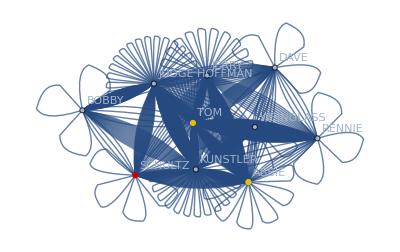

{DAVE,WEINGLASS,RENNIE,BOBBY,JERRY,SCHULTZ,ABBIE,JUDGE HOFFMAN,TOM,KUNSTLER}

```mathematica
HighlightGraph[TopgGrapUndirect1,{{"SCHULTZ"},{"ABBIE","TOM"}}]
vTop8 = VertexList[TopgGrapUndirect1]
```

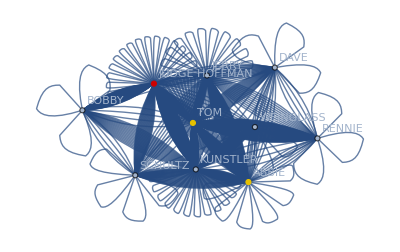

{DAVE,WEINGLASS,RENNIE,BOBBY,JERRY,SCHULTZ,ABBIE,JUDGE HOFFMAN,TOM,KUNSTLER}

```mathematica
HighlightGraph[TopgGrapUndirect1,{{"JUDGE HOFFMAN"},{"ABBIE","TOM"}}]
vTop8 = VertexList[TopgGrapUndirect1]
```

```mathematica
VertexIndex[TopgGrapUndirect1, {"DAVE","WEINGLASS","RENNIE","BOBBY","JERRY","SCHULTZ","ABBIE","JUDGE HOFFMAN","TOM","KUNSTLER"}]
```

{1,2,3,4,5,6,7,8,9,10}

## To highlight the different groups according the Parition

{2,2,2,1,2,1,2,1,2,2}

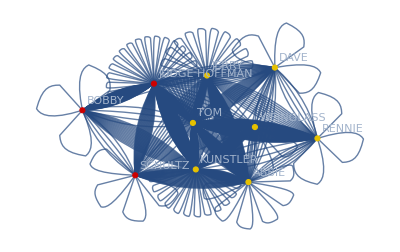

```mathematica
o1=Ordering[#][[1]]&/@FromMetricspaceS2DecisionMatric[MatUnDirect,{{6},{7}}]
HighlightGraph[TopgGrapUndirect1,{vTop8[[Flatten[Position[o1,1]]]],vTop8[[Flatten[Position[o1,2]]]]}]
```

VOTING ALGO
We can transform a Frequency graph to a Markov process by simple normalize the Frequency  (on TopgGrapDirect3)

```mathematica
FromGtoMarkve[G_]:=Module[{WA,M},(*The input is a Grapg G The output is Transition Matrix M*)WA=WeightedAdjacencyMatrix[G];(*Converts the graph in to weighted Adjacency matrix*)M=#/Total[#]&/@Normal[WA] (*Converts the weighted Adjacency matrix in to transition Markov matrix*)];
```

```mathematica
FromGtoMarkve[TopgGrapDirect3]
MatrixForm[%];
```

{{3/29,2/29,2/29,0,5/29,0,2/29,4/29,9/29,2/29},{1/25,2/25,0,0,1/25,0,2/25,3/25,7/25,9/25},{2/47,2/47,3/47,0,7/47,0,3/47,0,28/47,2/47},{0,0,0,3/47,1/47,0,0,32/47,2/47,9/47},{3/62,0,2/31,0,11/62,3/62,11/31,3/62,5/31,3/31},{0,1/40,0,1/10,1/8,1/10,11/40,9/40,1/40,1/8},{4/91,3/91,3/91,0,19/91,16/91,6/91,1/13,18/91,15/91},{6/119,3/119,0,27/119,3/119,16/119,12/119,16/119,9/119,27/119},{9/139,7/139,31/139,2/139,10/139,1/139,19/139,10/139,13/139,37/139},{1/65,1/13,1/65,4/65,3/130,3/65,6/65,37/130,19/65,6/65}}

## Here we change manually vector 6-7 which are our anchors

```mathematica
MatDecsion ={{3/29,2/29,2/29,0,5/29,0,2/29,4/29,9/29,2/29},{1/25,2/25,0,0,1/25,0,2/25,3/25,7/25,9/25},{2/47,2/47,3/47,0,7/47,0,3/47,0,28/47,2/47},{0,0,0,3/47,1/47,0,0,32/47,2/47,9/47},{3/62,0,2/31,0,11/62,3/62,11/31,3/62,5/31,3/31},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{6/119,3/119,0,27/119,3/119,16/119,12/119,16/119,9/119,27/119},{9/139,7/139,31/139,2/139,10/139,1/139,19/139,10/139,13/139,37/139},{1/65,1/13,1/65,4/65,3/130,3/65,6/65,37/130,19/65,6/65}}
```

{{3/29,2/29,2/29,0,5/29,0,2/29,4/29,9/29,2/29},{1/25,2/25,0,0,1/25,0,2/25,3/25,7/25,9/25},{2/47,2/47,3/47,0,7/47,0,3/47,0,28/47,2/47},{0,0,0,3/47,1/47,0,0,32/47,2/47,9/47},{3/62,0,2/31,0,11/62,3/62,11/31,3/62,5/31,3/31},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{6/119,3/119,0,27/119,3/119,16/119,12/119,16/119,9/119,27/119},{9/139,7/139,31/139,2/139,10/139,1/139,19/139,10/139,13/139,37/139},{1/65,1/13,1/65,4/65,3/130,3/65,6/65,37/130,19/65,6/65}}

### Multiply matrix by  a vector that represent character 
we do it for each character ans see what he choose to “vote” to

```mathematica
VertexList[TopgGrapDirect3];
```

```mathematica
{"DAVE","WEINGLASS","RENNIE","BOBBY","JERRY","SCHULTZ","ABBIE","JUDGE HOFFMAN","TOM","KUNSTLER"}
VertexIndex[TopgGrapDirect3, {"DAVE","WEINGLASS","RENNIE","BOBBY","JERRY","SCHULTZ","ABBIE","JUDGE HOFFMAN","TOM","KUNSTLER"}]
```

{DAVE,WEINGLASS,RENNIE,BOBBY,JERRY,SCHULTZ,ABBIE,JUDGE HOFFMAN,TOM,KUNSTLER}

{1,2,3,4,5,6,7,8,9,10}

```mathematica
(* 1. Dave choose  -- > ABBIE *)
{1,0,0,0,0,0,0,0,0,0}.MatrixPower[MatDecsion,100]//N
```

{2.18479×10^-9,2.23119×10^-9,3.43546×10^-9,3.49754×10^-9,3.2843×10^-9,0.230343,0.769657,8.97014×10^-9,9.76529×10^-9,8.9502×10^-9}

```mathematica
(*2. WEINGLASS choose  -- > ABBIE*)
{0,1,0,0,0,0,0,0,0,0}.MatrixPower[MatDecsion,100]//N
```

{2.27226×10^-9,2.32051×10^-9,3.57299×10^-9,3.63756×10^-9,3.41578×10^-9,0.251706,0.748294,9.32924×10^-9,1.01562×10^-8,9.30851×10^-9}

```mathematica
(*3. RENNIE choose  -- > ABBIE*)
{0,0,1,0,0,0,0,0,0,0}.MatrixPower[MatDecsion,100]//N
```

{2.23746×10^-9,2.28497×10^-9,3.51827×10^-9,3.58185×10^-9,3.36347×10^-9,0.210141,0.789859,9.18637×10^-9,1.00007×10^-8,9.16596×10^-9}

```mathematica
(*4. BOBBY choose  -- > ABBIE*)
{0,0,0,1,0,0,0,0,0,0}.MatrixPower[MatDecsion,100]//N
```

{2.37921×10^-9,2.42973×10^-9,3.74117×10^-9,3.80878×10^-9,3.57656×10^-9,0.34403,0.65597,9.76836×10^-9,1.06343×10^-8,9.74666×10^-9}

```mathematica
(*5. JERRY choose -- > ABBIE *)
{0,0,0,0,1,0,0,0,0,0}.MatrixPower[MatDecsion,100]//N
```

{1.3402×10^-9,1.36866×10^-9,2.10739×10^-9,2.14547×10^-9,2.01466×10^-9,0.190027,0.809973,5.50248×10^-9,5.99025×10^-9,5.49025×10^-9}

```mathematica
(*6. SCHULTZ choose ---- > SCHULTZ itself, he is anchor*)
{0,0,0,0,0,1,0,0,0,0}.MatrixPower[MatDecsion,100]//N
```

{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.}

```mathematica
(*7. ABBIE choose --- > ABBIE itself, he is anchor*)
{0,0,0,0,0,0,1,0,0,0}.MatrixPower[MatDecsion,100]//N
```

{0.,0.,0.,0.,0.,0.,1.,0.,0.,0.}

```mathematica
(*8. "JUDGE HOFFMAN" choose --- > ABBIE *)
{0,0,0,0,0,0,0,1,0,0}.MatrixPower[MatDecsion,100]//N
```

{1.95189×10^-9,1.99334×10^-9,3.06923×10^-9,3.1247×10^-9,2.93419×10^-9,0.369443,0.630557,8.01391×10^-9,8.7243×10^-9,7.9961×10^-9}

```mathematica
(*9. "TOM" choose   --- > ABBIE*)
{0,0,0,0,0,0,0,0,1,0}.MatrixPower[MatDecsion,100]//N
```

{2.1226×10^-9,2.16767×10^-9,3.33766×10^-9,3.39798×10^-9,3.19081×10^-9,0.227085,0.772915,8.71479×10^-9,9.48731×10^-9,8.69543×10^-9}

```mathematica
(*10. "KUNSTLER" choose  --- > ABBIE*)
{0,0,0,0,0,0,0,0,0,1}.MatrixPower[MatDecsion,100]//N
```

{2.12515×10^-9,2.17028×10^-9,3.34167×10^-9,3.40206×10^-9,3.19464×10^-9,0.296771,0.703229,8.72526×10^-9,9.49871×10^-9,8.70588×10^-9}

### Another way from lecture to represent VOTING result

```mathematica
FromABG2LinearSys[G_,A_,B_]:=
(* The input is a gragp G and two sets of nodes anchors A,B. The output is {M,b} Solving the systems M.Π=z is the will give the propblity to vote to Party A *)
Module[{n=VertexCount[G],i,v,z,b},
(* n numbers of nodes, i index, v is normalistion factors, z is a contant vectors  *)
z=Table[0,{i,1,n}]; (* Initialization z, most of the Coefficient in z are 0 *)
b=Table[-1,{i,1,n}]; (* Transfer the variables to the side of the matrix M *)
v=1/(VertexOutDegree[G]); (* v is normalistion acording to simple random walks *)
(* The next five lines deal with anchor nods that we know their opinions i.e. A and B *)
v[[A]]=0;
z[[A]]=1;
v[[B]]=0;
b[[A]]=1;
b[[B]]=1;
{DiagonalMatrix[v].AdjacencyMatrix[G]+DiagonalMatrix[b],z} (* output {M,z}*)
];
Votkp[G_,P1_]:=
(* The input is a graph and k-subsets of an anchors. Output is the ψ decision matrix of the voting algorithm*)
Module[{lab,ψ,i,k=Length[P1]},
ψ={};
For[i=1,i≤ k,i++, (* going over all k parties *)
lab=FromABG2LinearSys[G,P1[[i]],Complement[Union[Flatten[P1]],P1[[i]]]]; (* compue the vote Linear systeam for a i-party *)
AppendTo[ψ,LinearSolve[lab[[1]], lab[[2]]]]//N;  (* compue the propability to vote for a party i *)
];
Transpose[ψ]
];
```

```mathematica
Votkp[TopgGrapDirect3,{{6},{7}}]
MatrixForm[%]
```

{{861186056049/3738719332547,2877533276498/3738719332547},{941056638713/3738719332547,2797662693834/3738719332547},{785657948501/3738719332547,2953061384046/3738719332547},{1286230842663/3738719332547,2452488489884/3738719332547},{710458738128/3738719332547,3028260594419/3738719332547},{1,0},{0,1},{44556251828/120603849437,76047597609/120603849437},{849005990110/3738719332547,2889713342437/3738719332547},{1109542727272/3738719332547,2629176605275/3738719332547}}

(861186056049/3738719332547 | 2877533276498/3738719332547
941056638713/3738719332547 | 2797662693834/3738719332547
785657948501/3738719332547 | 2953061384046/3738719332547
1286230842663/3738719332547 | 2452488489884/3738719332547
710458738128/3738719332547 | 3028260594419/3738719332547
1 | 0
0 | 1
44556251828/120603849437 | 76047597609/120603849437
849005990110/3738719332547 | 2889713342437/3738719332547
1109542727272/3738719332547 | 2629176605275/3738719332547)

```mathematica
vTop8Direct=VertexList[TopgGrapDirect3]
```

{DAVE,WEINGLASS,RENNIE,BOBBY,JERRY,SCHULTZ,ABBIE,JUDGE HOFFMAN,TOM,KUNSTLER}

{1,1,1,1,1,2,1,1,1,1}

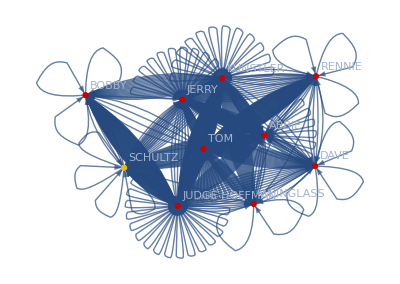

```mathematica
o1=Ordering[#][[1]]&/@Votkp[TopgGrapDirect3,{{6},{7}}]
HighlightGraph[TopgGrapDirect3,{vTop8Direct[[Flatten[Position[o1,1]]]],vTop8Direct[[Flatten[Position[o1,2]]]]}]
```

### Now we see all the other implemented  algorithm there are (we saw on lecture)

```mathematica
options={"Modularity","Centrality","CliquePercolation","Hierarchical","Spectral","VertexMoving"};
```

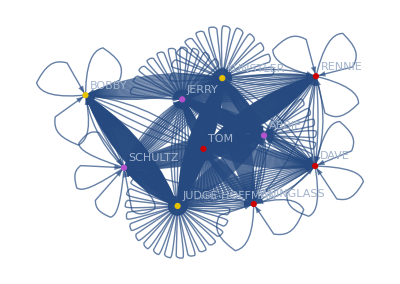
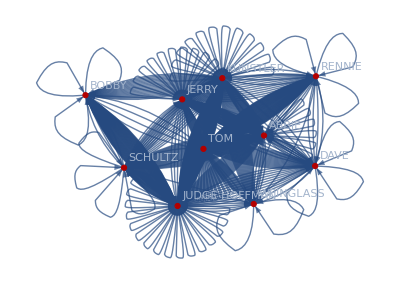
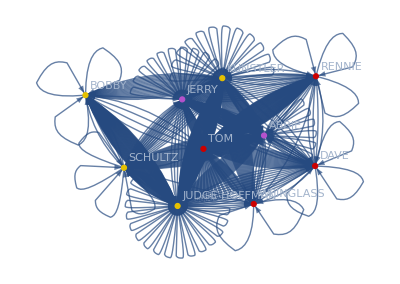
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightGraph[TopgGrapDirect3,FindGraphCommunities[TopgGrapDirect3,Method->#]]&/@options
```